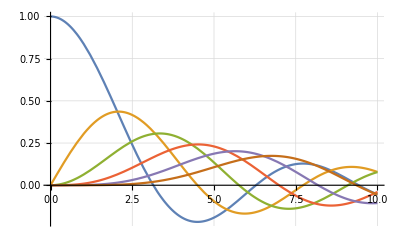

```mathematica
SphericalBesselJ[n, x]/.n:> #&/@Range[0,5]//Plot[#, {x, 0,10},
PlotRange->All,
GridLines->Automatic
]&
```

```mathematica
FindPeaks
```

```mathematica
FindMaximum[SphericalBesselJ[2, x], {x, 2}]
```

{0.306792,{x→3.34209}}